```mathematica
qsupp
```

1.18373×10^10

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

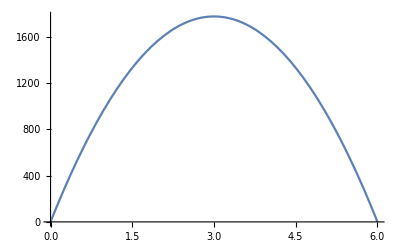

```mathematica
L=6 10^-7;
yp1=L/3;
yp2=2 L/3;
q1=1.6 10^-19;
q2=1.6 10^-19;
ϵ=586.66 10^-21;
eq1=ϵ D[ϕ[y],{y,2}]==q1 DiracDelta[y-yp1];
eq2=ϵ D[ϕ[y],{y,2}]==-2q1 /(L(8L)^2);
eq3=ϵ D[ϕ[y],{y,2}]==2/L;
grad=(2 1.6 10^-19/(2(8L)^2 ϵ))
(*func1[y_]=DSolve[{eq2,ϕ[0]==1 ,ϕ[L]==1},ϕ[y],y][[1,1,2]];*)
func2[y_]=NDSolve[{eq2,ϕ'[0]==grad ,ϕ'[L]==-grad},ϕ[y],y][[1,1,2]];
Plot[func2[y],{y,0,L}]
```

```mathematica
bforce[q_,y_]=-q func2'[y]
```

-q InterpolatingFunction[…][y]

```mathematica
(2 1.6 10^-19/(2(8L)^2))
```

6.94444×10^-9

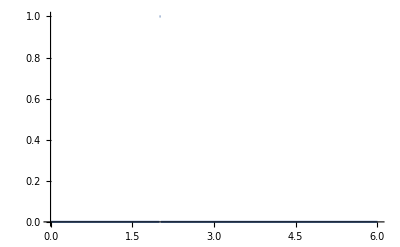

```mathematica
Plot[HeavisideTheta[y-yp1]-HeavisideTheta[y-yp1-0.01yp1],{y,0,L}]
```

```mathematica
potentialFunc[r_,x_,c1_]:=1/(4π ϵ)c1/(((r[[1]]-x[[1]])^2+(r[[2]]-x[[2]])^2)^(1/2));
gradFunc[r_,x_,c1_]:=-(c1 (r[[2]]-x[[2]]))/(4 π ((r[[1]]-x[[1]])^2+(r[[2]]-x[[2]])^2)^(3/2) ϵ);
ϵ=586.66 10^-21;
lp=10000000;
lp=0;
rp=0;
L=6.0 10^-7;
grad =(2 1.6 10^-19/(2(8L)^2 ϵ));
grad=0;
dx=L/64;
qp=1.6 10^-19;
qn=-1.6 10^-19;
qTab={qp,qp};
pTab={{0,0.1875dx },{2dx,0.1875dx }};
images=500;
bottomPos={{pTab[[1,1]],-pTab[[1,2]]},{pTab[[2,1]],-pTab[[2,2]]}};
topPos={{pTab[[1,1]],L+(L-pTab[[1,2]])},{pTab[[2,1]],L+(L-pTab[[2,2]])}};
bottomImages={Solve[gradFunc[{pTab[[1,1]],0},pTab[[1]],qTab[[1]]]+gradFunc[{pTab[[1,1]],0},bottomPos[[1]],q]==-grad,q][[1,1,2]],Solve[gradFunc[{pTab[[2,1]],0},pTab[[2]],qTab[[2]]]+gradFunc[{pTab[[2,1]],0},bottomPos[[2]],q]==-grad,q][[1,1,2]]}
topImages={Solve[gradFunc[{pTab[[1,1]],L},pTab[[1]],qTab[[1]]]+gradFunc[{pTab[[1,1]],L},topPos[[1]],q]==grad,q][[1,1,2]],Solve[gradFunc[{pTab[[2,1]],L},pTab[[2]],qTab[[2]]]+gradFunc[{pTab[[2,1]],L},topPos[[2]],q]==grad,q][[1,1,2]]}


For[i=1,i<=images,i++,
bp={topPos[[i,1]],-topPos[[i,2]]};
tp={bottomPos[[i,1]],L+(L-bottomPos[[i,2]])};
bq=topImages[[i]];
tq=bottomImages[[i]];
AppendTo[topPos,tp];
AppendTo[bottomPos,bp];
AppendTo[topImages,tq];
AppendTo[bottomImages,bq];
]
```

{1.6×10^-19,1.6×10^-19}

{1.6×10^-19,1.6×10^-19}

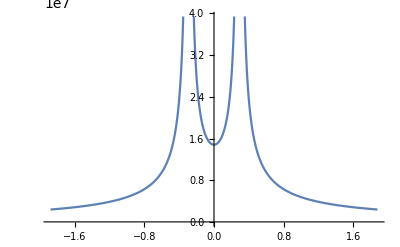

```mathematica
Plot[potentialFunc[{pTab[[1,1]],r},pTab[[1]],qp]+potentialFunc[{bottomPos[[1,1]],r},bottomPos[[1]],bottomImages[[1]]],{r,-2dx,2dx}]
```

```mathematica
forceFunc[y_,c1_,c2_]=1/(4π ϵ)(c1 c2)/(y.y)y/Norm[y];
gradFunc[{1dx,0},pTab[[1]],qp]+gradFunc[{0.25bottomPos[[1,1]],0},bottomPos[[1]],bottomImages[[1]]]
```

-2.46152×10^15

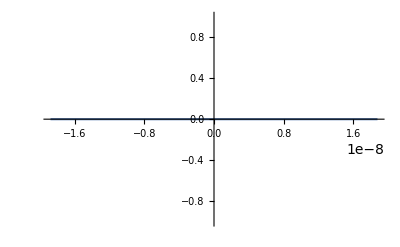

```mathematica
Plot[gradFunc[{r,0},pTab[[1]],qp]+gradFunc[{r,0},bottomPos[[1]],bottomImages[[1]]],{r,-2dx,2dx}]
```

```mathematica
D[func2[y],y]/.y->0
```

-0.27273

```mathematica
D[potentialFunc[{pTab[[1,1]],r},pTab[[1]],qp]+potentialFunc[{bottomPos[[1,1]],r},bottomPos[[1]],bottomImages[[1]]],r]/.r->0
```

-1.18373×10^10

```mathematica
Norm[dx^2 4 π ϵ (Sum[forceFunc[pTab[[1]]-topPos[[ii]],qTab[[1]],topImages[[ii]]],{ii,1,images+2}]+Sum[forceFunc[pTab[[1]]-bottomPos[[ii]],qTab[[1]],bottomImages[[ii]]],{ii,1,images+2}]+{0,-(rp-lp)/L qTab[[1]]}+forceFunc[pTab[[1]]-pTab[[2]],qTab[[1]],qTab[[2]]]+bforce[qTab[[1]],pTab[[1,2]]])/(qTab[[1]]^2)]
```

7.17215

```mathematica
data=Import["/home/drladiges/gigan/projects/FHDeX/exec/immersedIons/threepmForce"];
mean =dx^2 4 π ϵ Mean[data[[All,2]]]/(qTab[[1]]^2)
max=dx^2 4 π ϵ Max[data[[All,2]]]/(qTab[[1]]^2)
min=dx^2 4 π ϵ Min[data[[All,2]]]/(qTab[[1]]^2)
```

7.1533

7.15393

7.15279

```mathematica
dx^2 4 π ϵ bforce[qTab[[1]],pTab[[1,2]]]/(qTab[[1]]^2)
```

0.0000232194

```mathematica
(1.6 10^-19/(2(8L)^2 ϵ))
```

5.91863×10^9

```mathematica
1.1837255726390833*^10
```

```mathematica
qu=Solve[gradFunc[0,2dx,qp]+gradFunc[0,-2dx,q]==grad/2,q][[1,1,2]]
```

-1.60015×10^-19

```mathematica
gradFunc[0,2dx,qp]
```

-0.0000362166/ϵ

```mathematica
qp
```

1.6×10^-19

```mathematica
grad/2
```

5.91863×10^9

```mathematica
Plot[gradFunc[r,2dx,qp]+gradFunc[r,-2dx,qu],{r,-3dx,3dx}]
```

-Graphics-

```mathematica
dx^2 4 π ϵ forceFunc[{0,4dx},qp,qu][[2]]/(qp qu)
```

0.0625

```mathematica
5.918627863195416*^9
```

```mathematica
gradFunc[r,y,q]
```

-(1.35645×10^17 q)/r^2-(1.35645×10^17 y)/r^2

```mathematica
Remove[potentialFunc];
Clear[ϵ]
potentialFunc[rx_,ry_,rz_,x_,y_,z_,c1_]=1/(4π ϵ)c1/(((rx-x)^2+(ry-y)^2+(rz-z)^2)^(1/2));
gradFunc[r_,y1_,c1_]=-(c1 (rx-x))/(4 π ((rx-x)^2+(ry-y)^2+(rz-z)^2)^(3/2) ϵ);
```

```mathematica
D[potentialFunc[rx,ry,rz,x,y,z,c1],rx]
```

-(c1 (rx-x))/(4 π ((rx-x)^2+(ry-y)^2+(rz-z)^2)^(3/2) ϵ)

```mathematica
potentialFunc[1,1,1,1,1,1,1]
```

Power::infy: Infinite expression 1/(√0) encountered.

ComplexInfinity